```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Functions

```mathematica
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont=SetPrecision[{0.5129548374487685,0.002435119807500435},30];(*10k run*)
σcont=SetPrecision[{0.16999653850906107,0.000838106749908169},30];
ccont=SetPrecision[{-0.1611740456186636,0.002474788649682089},30];
```

### Self energies

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
```

```mathematica
Πpar[θ_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]),30];
```

### IIT paper

#### Potentials

```mathematica
ReVcpp[r_,mD_,u_,α_,c_]:=Re[c-α/r+α  NIntegrate[Sin[θ] √Πpar[θ,mD,u] Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVspp[r_,mD_,u_,σ_]:=Re[σ NIntegrate[Sin[θ] 1/(√Πpar[θ,mD,u])Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVsp[r_,mD_,u_,σ_]:=σ NIntegrate[Sin[θ] 1/Re[√Πpar[θ,mD,u]] Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*WE USE THIS ONE*)
ReVcp[r_,mD_,u_,α_,c_]:=c-α mD-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,mD,u]] Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*OUR MODEL DIFFERS HERE*)
```

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=2 α T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])(Sinh[√Πpar[x,mD,u] r Cos[x]]SinhIntegral[√Πpar[x,mD,u] r Cos[x]]-Cosh[√Πpar[x,mD,u] r Cos[x]]CoshIntegral[√Πpar[x,mD,u] r Cos[x]]-Sinh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]),{x,0,π/2},MaxRecursion->20,WorkingPrecision->20];
```

#### Permittivities

```mathematica
ϵRepp[r_,mD_,u_]:=Re[1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Πpar[θ,mD,u]Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Πpar[θ,mD,u]^(3/2)Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}])];(*INCORRECT*)
ϵRep[r_,mD_,u_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,mD,u]]Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,mD,u]]^(3/2)Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]);(*WE USE THIS ONE*)
```

```mathematica
Integrate[-4π σ r^2/(4π)(2/r Cos[θ]Sin[θ]Re[Πpar[θ,mD,u]]Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]]-Cos[θ]^2 Sin[θ] Re[Πpar[θ,mD,u]]^(3/2)Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]]),r]//Simplify
```

-ⅇ^(-r Cos[θ] √Re[Πpar[θ,mD,u]]) r^2 σ Cos[θ] Re[Πpar[θ,mD,u]] Sin[θ]

```mathematica
ϵRepr1[r_,mD_,u_,θ_,σ_]:=-ⅇ^(-r Cos[θ] √Re[Πpar[θ,mD,u]]) r^2 σ Cos[θ] Re[Πpar[θ,mD,u]] Sin[θ];(*WE ACTUALLY USE THIS ONE*)
```

```mathematica
ϵImp[r_,mD_,u_,T_]:=Re[1/(2π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])1/r Cos[x] (2 √Conjugate[Πpar[x,mD,u]] (CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]] Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+r Conjugate[Πpar[x,mD,u]] Cos[x] (Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+√Πpar[x,mD,u] (-CoshIntegral[r Cos[x] √Πpar[x,mD,u]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,mD,u]] √Πpar[x,mD,u]+2 Sinh[r Cos[x] √Πpar[x,mD,u]])+(2 Cosh[r Cos[x] √Πpar[x,mD,u]]+r Cos[x] √Πpar[x,mD,u] Sinh[r Cos[x] √Πpar[x,mD,u]]) SinhIntegral[r Cos[x] √Πpar[x,mD,u]])),{x,0,π/2},WorkingPrecision->20]];(*UNREGULATED*)
```

```mathematica
ϵImRreg[r_,mD1_,u1_,T1_,Δ1_]:=Block[{mD=mD1,T=T1,u=u1,Δ=Δ1,temp,inter},temp=Join[ParallelTable[Quiet[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]}],{p,10^-10,10,1/1000}],ParallelTable[Quiet[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]}],{p,101/10,200,1/10}]];
inter=Interpolation[temp];
Return[-(2 π^2 T mD^2)/(2π)^3 NIntegrate[inter[x],{x,0,200}]]]
```

```mathematica
temp=Table[{r,ϵImRreg[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],5/10,0.155,reg mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]]]},{r,10^-10,10,1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.617396}. NIntegrate obtained 0.309976+2.85866×10^-16 ⅈ and 3.22471×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.617396}. NIntegrate obtained 0.143401+9.61663×10^-18 ⅈ and 1.64389×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {17.575}. NIntegrate obtained 0.067929-3.07244×10^-16 ⅈ and 1.55348×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

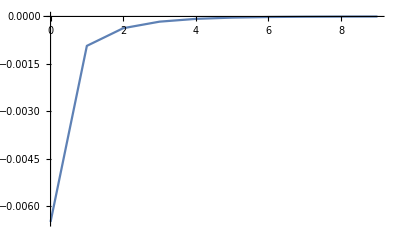

```mathematica
ListPlot[temp,Joined->True,PlotRange->All]
```

### Tabs for ReΠ>0

```mathematica
ReVsTab[mD1_,u1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,tab0,tab,inter0,inter1,inter},tab0=ParallelTable[{r,σ+NIntegrate[ϵRepr1[r,mD,u,θ,σ],{θ,0,π/2}]},{r,10^-10,500,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
tab=ParallelTable[{r,inter1[r]},{r,0,500,1/100}];
Export["mathematica/vel_pot/ReVsu"<>ToString[Round[100 u]]<>".dat",tab];
Return[Interpolation[tab]]];
```

```mathematica
reg=303689/100000;
```

```mathematica
ImVsTab[mD1_,u1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=Table[{r,4π σ r^2 ϵImRreg[r,mD,u,T,reg mD]},{r,10^-10,100,1/10}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,10^-10,r}];
temp=inter1[10^-10];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,100,1/10}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,10^-10,r}];
tab2=ParallelTable[{r,inter2[r]},{r,10^-10,100,1/10}];
Export["mathematica/vel_pot/ImVsRegu"<>ToString[Round[100 u]]<>".dat",tab2];];
```

### Potential for mixed ReΠ

```mathematica
ReVcMixed[r_,mD_,u_,α_,c_]:=Block[{θcut,int1,int2},θcut=x/.FindRoot[Re[Πpar[x,mD,u]]==0,{x,1.5}];int1=NIntegrate[2α(-Re[Πpar[θ,mD,u]])^(3/2)Sin[θ]Sin[r Cos[θ] √(-Re[Πpar[θ,mD,u]])],{θ,0,θcut}];
int2=ccont[[1]]-α mD-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,mD,u]] Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,θcut,π/2}];
Return[int1+int2]];
```

```mathematica
Block[{α=αcont[[1]],u=9/10,mD=2/10,r=3/(197/1000)},ccont[[1]]-α mD+α/π NIntegrate[Sin[x](p^2 Exp[ⅈ p r Cos[x]])/(p^2+Re[Πpar[x,mD,u]]),{p,0,∞},{x,0,π}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {0.117547,0.913296}. NIntegrate obtained -0.1693+0.00394785 ⅈ and 0.187805 for the integral and error estimates.

-0.291408+0.0006446 ⅈ

```mathematica
ReVcMixed[3/(197/1000),2/10,90/100,αcont[[1]],ccont[[1]]]
```

-0.262492

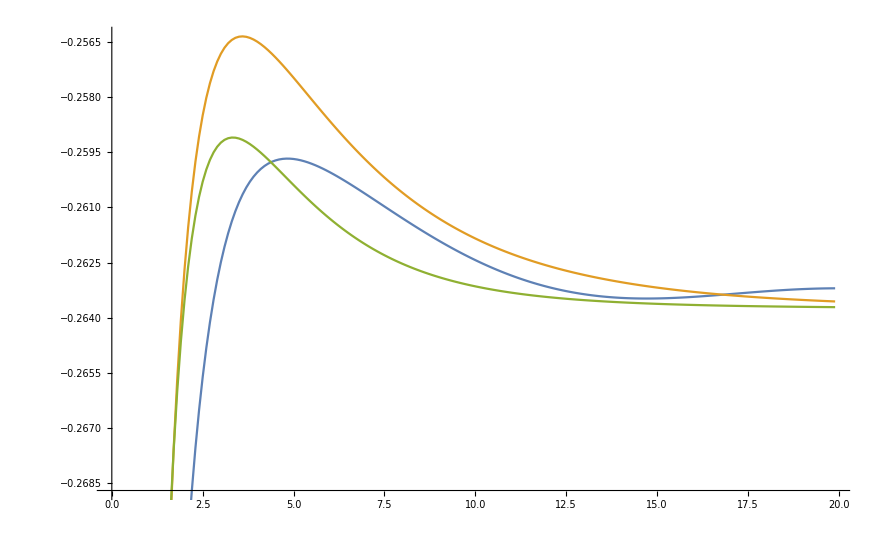

```mathematica
DiscretePlot[{Re[ReVcMixed[r/(197/1000),2/10,90/100,αcont[[1]],ccont[[1]]]],ReVcp[r/(197/1000),2/10,8/10,αcont[[1]],ccont[[1]]],ReVcp[r/(197/1000),2/10,7/10,αcont[[1]],ccont[[1]]]},{r,10^-10,20,1/10},Joined->True,Filling->None]
```

### Make potentials

```mathematica
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],1/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],2/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],3/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],4/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],5/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],6/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],7/10,σcont[[1]]];
ReVsTab[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],8/10,σcont[[1]]];
```

```mathematica
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],1/10,SetPrecision[σcont[[1]],30],155/1000];
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],2/10,SetPrecision[σcont[[1]],30],155/1000];
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],3/10,SetPrecision[σcont[[1]],30],155/1000];
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],4/10,SetPrecision[σcont[[1]],30],155/1000];
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],5/10,SetPrecision[σcont[[1]],30],155/1000];
```

```mathematica
Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],6/10,SetPrecision[σcont[[1]],30],155/1000]];
Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],7/10,SetPrecision[σcont[[1]],30],155/1000]];
Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],8/10,SetPrecision[σcont[[1]],30],155/1000]];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],1/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],1/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu10.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],3/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],3/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu30.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],3/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],3/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu30.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],4/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],4/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu40.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],5/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],5/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu50.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],6/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],6/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu60.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],7/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],7/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu70.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],8/10,SetPrecision[αcont[[1]],30],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],8/10,SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu80.dat",temp1];
```

```mathematica
Export["mathematica/vel_pot/ReVcu10.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],1/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}]],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],1/10,αcont[[1]],ccont[[1]]]}}];
Export["mathematica/vel_pot/ReVcu20.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],2/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],2/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu30.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],3/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],3/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu40.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],4/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],4/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu50.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],5/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],5/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu60.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],6/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],6/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu70.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],7/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],7/10,αcont[[1]],ccont[[1]]]}}]];
Export["mathematica/vel_pot/ReVcu80.dat",Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],8/10,αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],8/10,αcont[[1]],ccont[[1]]]}}]];
```

## Plot potentials

### T = 0.155 GeV

```mathematica
ReVsu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu10.dat"]]];
ReVsu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu20.dat"]]];
ReVsu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu30.dat"]]];
ReVsu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu40.dat"]]];
ReVsu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu50.dat"]]];
ReVsu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu60.dat"]]];
ReVsu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu70.dat"]]];
ReVsu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu80.dat"]]];
```

```mathematica
ReVcu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu10.dat"]]];
ReVcu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu20.dat"]]];
ReVcu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu30.dat"]]];
ReVcu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu40.dat"]]];
ReVcu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu50.dat"]]];
ReVcu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu60.dat"]]];
ReVcu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu70.dat"]]];
ReVcu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu80.dat"]]];
```

```mathematica
ImVcu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu10.dat"]]];
ImVcu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu20.dat"]]];
ImVcu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu30.dat"]]];
ImVcu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu40.dat"]]];
ImVcu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu50.dat"]]];
ImVcu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu60.dat"]]];
ImVcu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu70.dat"]]];
ImVcu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu80.dat"]]];
```

```mathematica
ImVsu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu10.dat"]]];
ImVsu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu20.dat"]]];
ImVsu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu30.dat"]]];
ImVsu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu40.dat"]]];
ImVsu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu50.dat"]]];
ImVsu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu60.dat"]]];
ImVsu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu70.dat"]]];
ImVsu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu80.dat"]]];
```

```mathematica
uSetS={"1/10","2/10","3/10","4/10","5/10","6/10","7/10","8/10"};
```

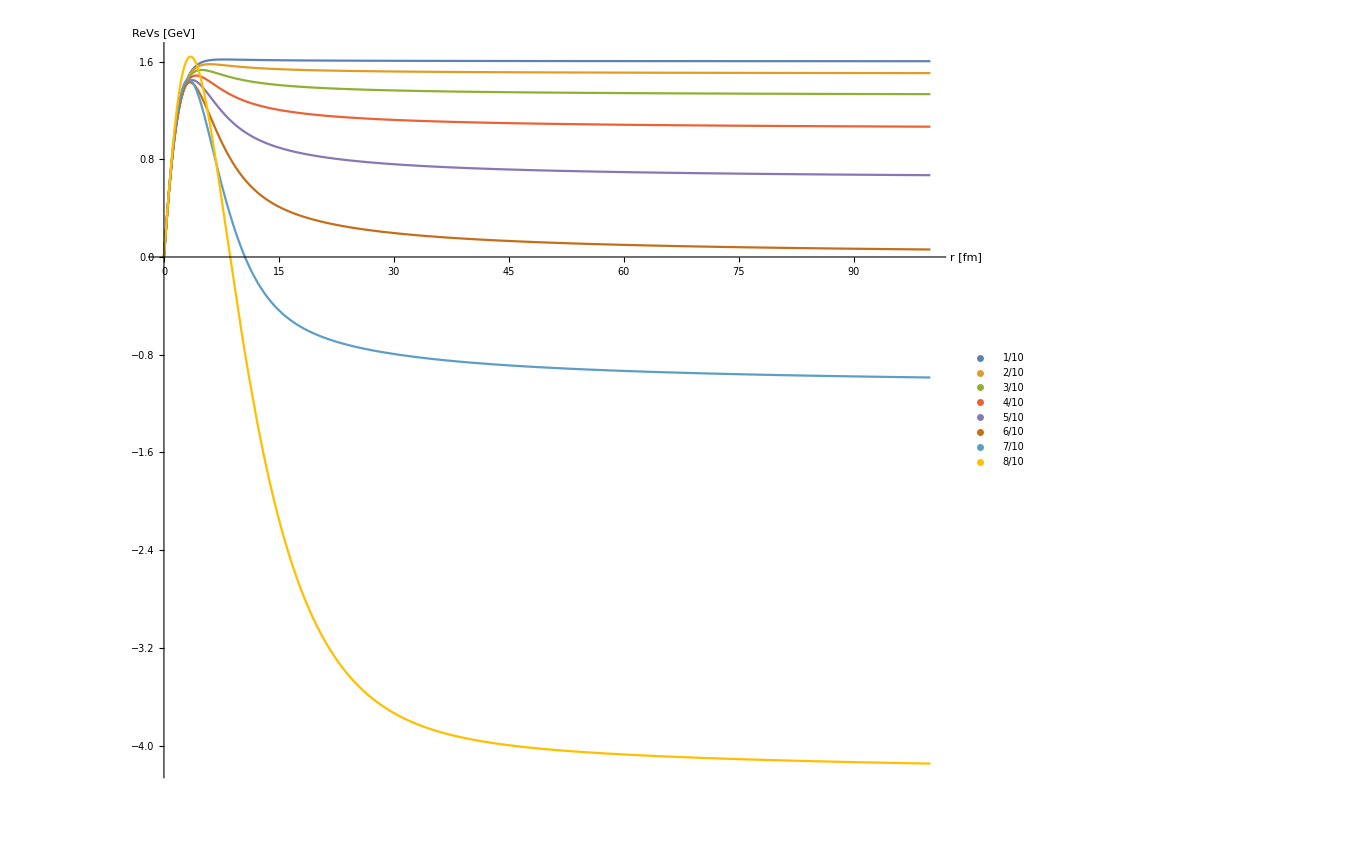

```mathematica
Plot[{ReVsu10[r/0.197],ReVsu20[r/0.197],ReVsu30[r/0.197],ReVsu40[r/0.197],ReVsu50[r/0.197],ReVsu60[r/0.197],ReVsu70[r/0.197],ReVsu80[r/0.197]},{r,0,100},PlotRange->All,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.2}],BaseStyle->{FontSize->14}]
```

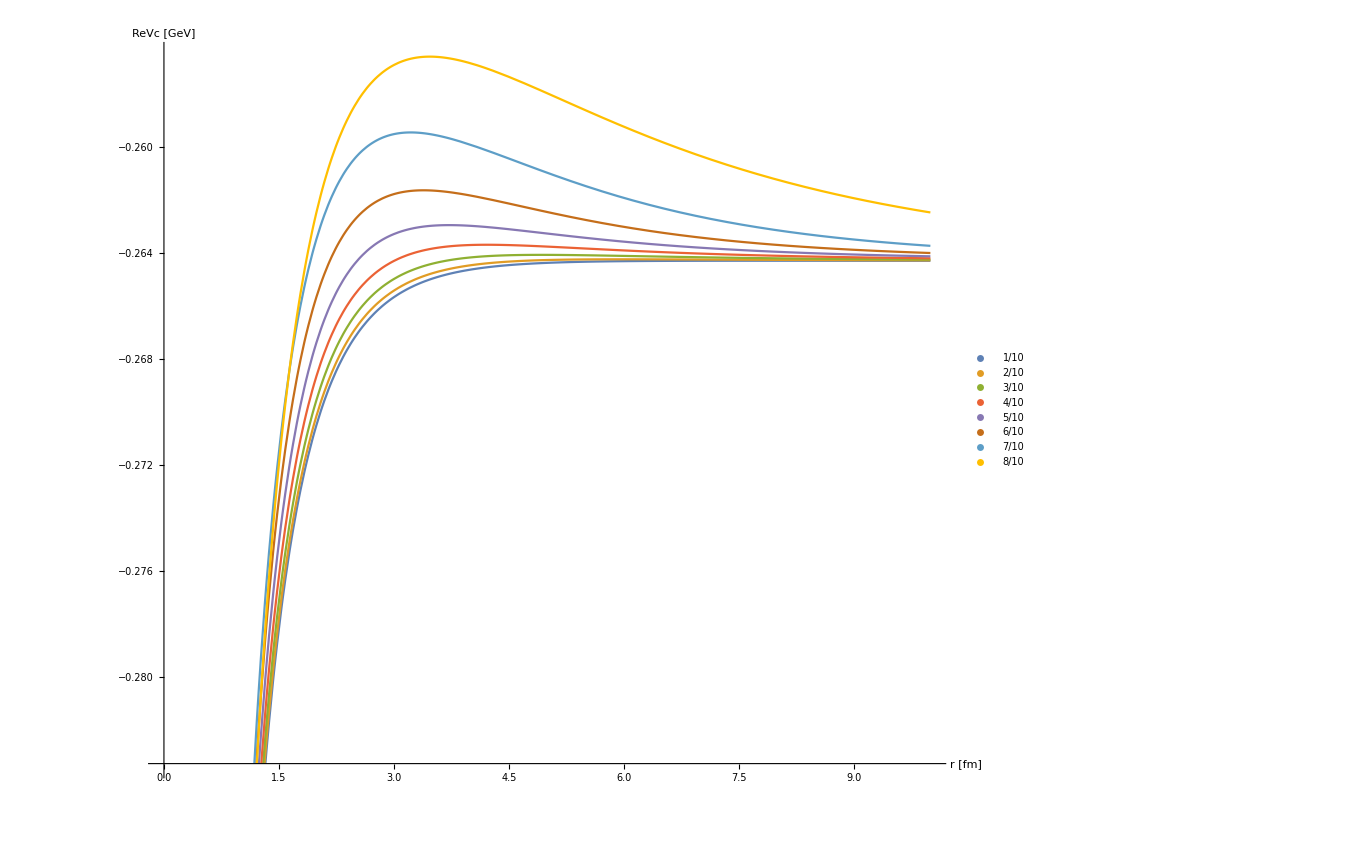

```mathematica
Plot[{ReVcu10[r/0.197],ReVcu20[r/0.197],ReVcu30[r/0.197],ReVcu40[r/0.197],ReVcu50[r/0.197],ReVcu60[r/0.197],ReVcu70[r/0.197],ReVcu80[r/0.197]},{r,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.3}],BaseStyle->{FontSize->14}]
```

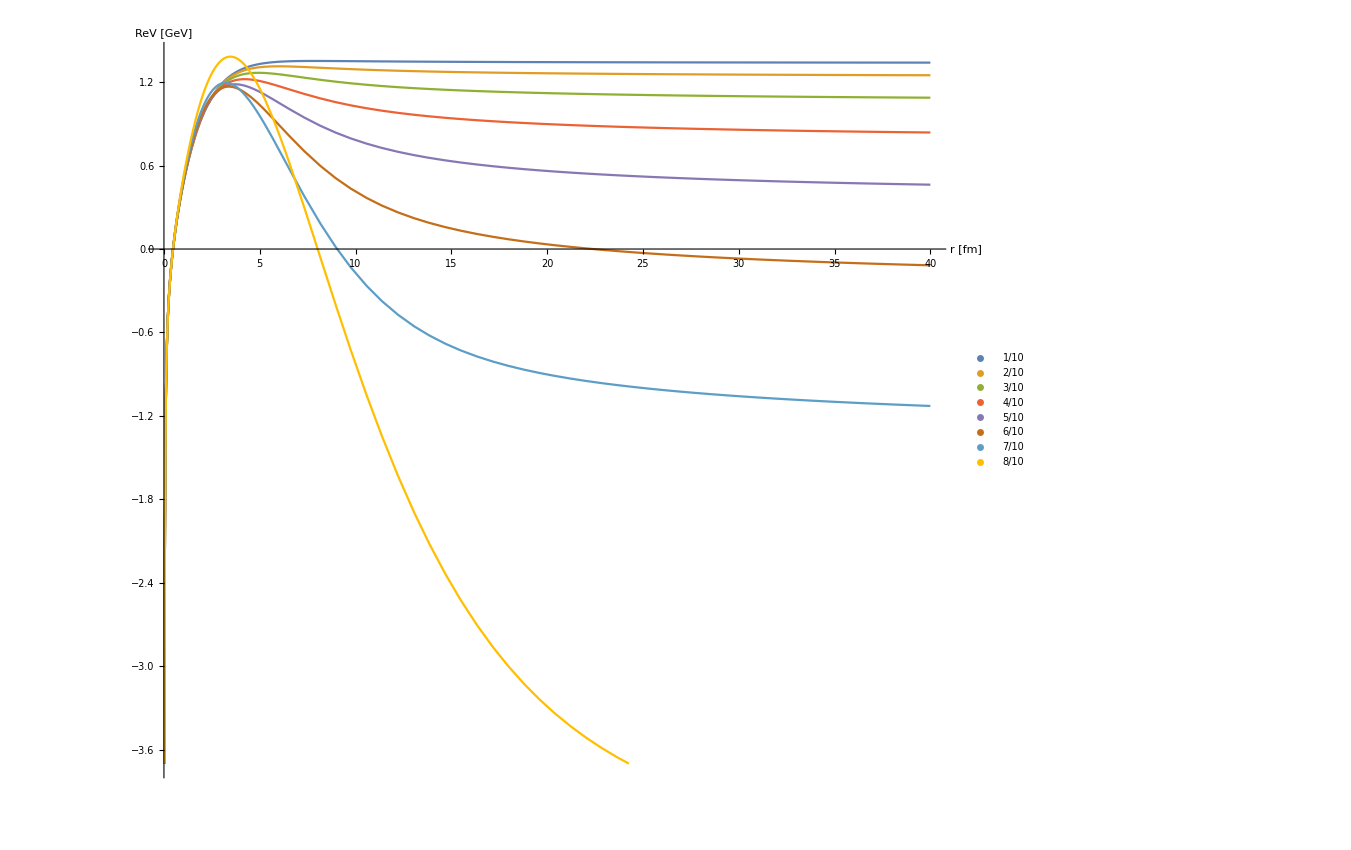

```mathematica
Plot[{ReVsu10[r/0.197]+ReVcu10[r/0.197],ReVcu20[r/0.197]+ReVsu20[r/0.197],ReVsu30[r/0.197]+ReVcu30[r/0.197],ReVsu40[r/0.197]+ReVcu40[r/0.197],ReVsu50[r/0.197]+ReVcu50[r/0.197],ReVsu60[r/0.197]+ReVcu60[r/0.197],ReVsu70[r/0.197]+ReVcu70[r/0.197],ReVsu80[r/0.197]+ReVcu80[r/0.197]},{r,0,40},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReV [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

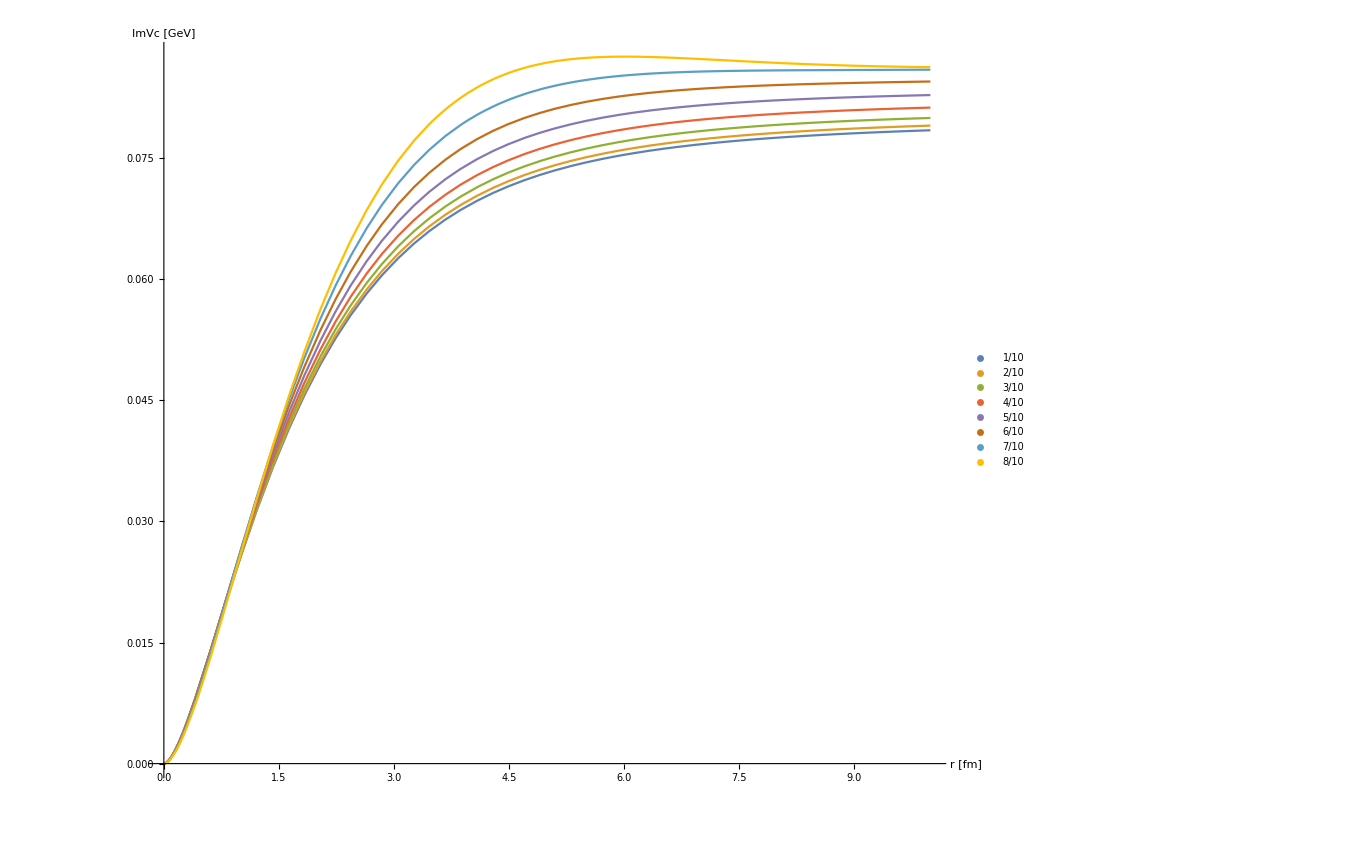

```mathematica
Plot[{Re[ImVcu10[r/0.197]],Re[ImVcu20[r/0.197]],Re[ImVcu30[r/0.197]],Re[ImVcu40[r/0.197]],Re[ImVcu50[r/0.197]],Re[ImVcu60[r/0.197]],Re[ImVcu70[r/0.197]],Re[ImVcu80[r/0.197]]},{r,1/1000,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

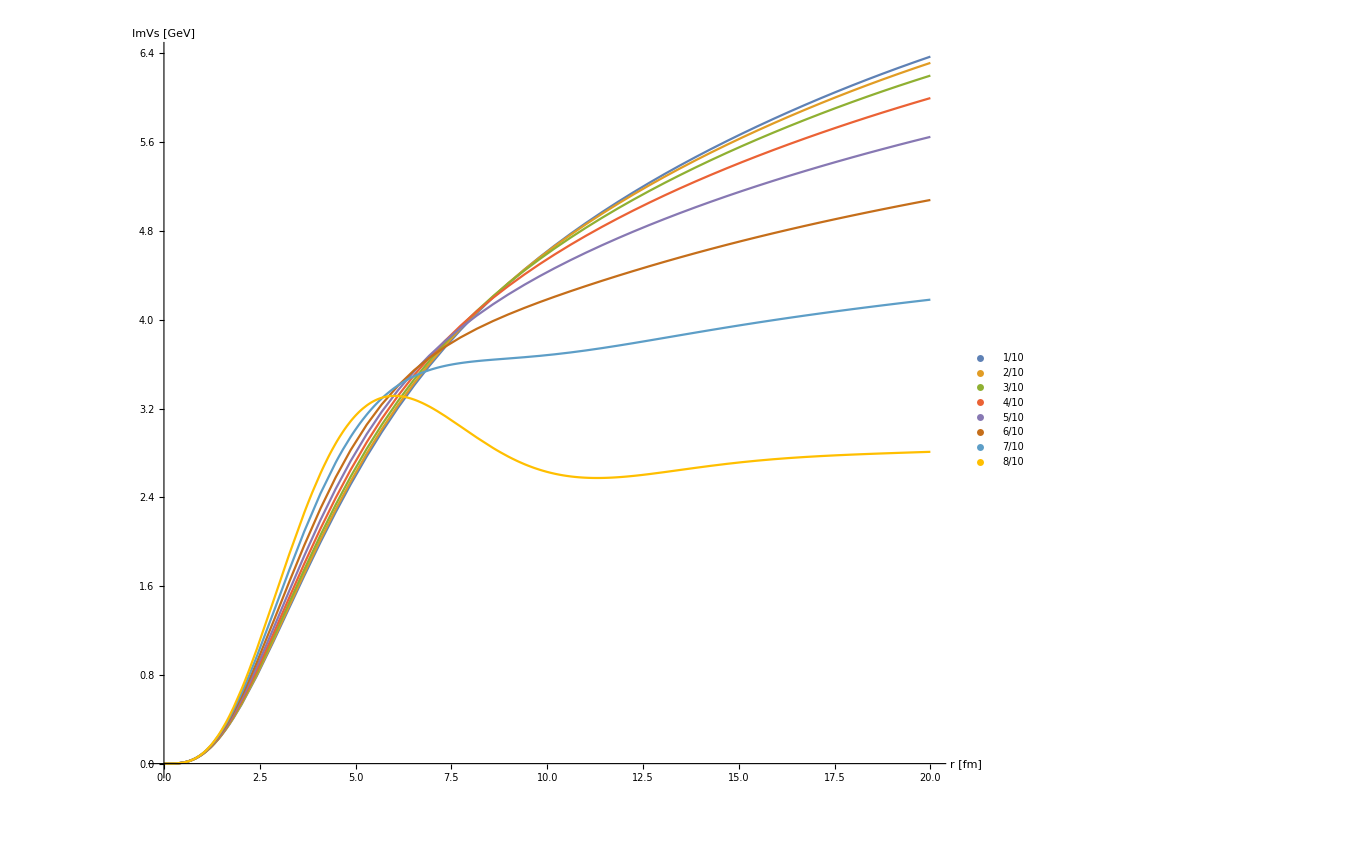

```mathematica
Plot[{ImVsu10[r/0.197],ImVsu20[r/0.197],ImVsu30[r/0.197],ImVsu40[r/0.197],ImVsu50[r/0.197],ImVsu60[r/0.197],ImVsu70[r/0.197],ImVsu80[r/0.197]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

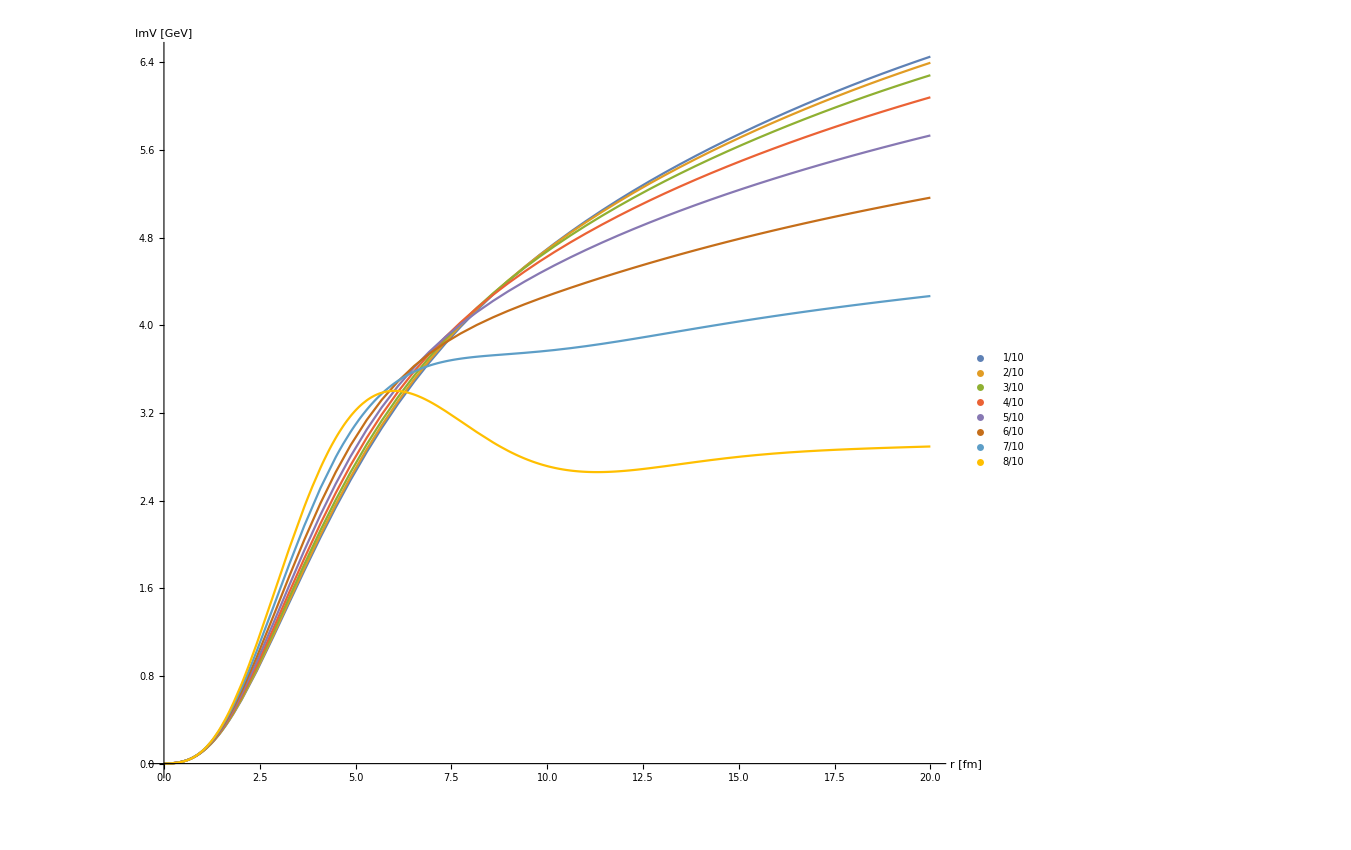

```mathematica
Plot[{ImVsu10[r/0.197]+ImVcu10[r/0.197],ImVsu20[r/0.197]+ImVcu20[r/0.197],ImVsu30[r/0.197]+ImVcu30[r/0.197],ImVsu40[r/0.197]+ImVcu40[r/0.197],ImVsu50[r/0.197]+ImVcu50[r/0.197],ImVsu60[r/0.197]+ImVcu60[r/0.197],ImVsu70[r/0.197]+ImVcu70[r/0.197],ImVsu80[r/0.197]+ImVcu80[r/0.197]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```